```mathematica
ϕ1[r1_]=(c0(r1-rc)^3+c1(r1-rc)^4+c2(r1-rc)^5)/((x-r1)(r1-re)^3(r1-rc)^3)
```

(c0 (r1-rc)^3+c1 (r1-rc)^4+c2 (r1-rc)^5)/((r1-rc)^3 (r1-re)^3 (-r1+x))

```mathematica
ϕ2[r1_]=(e0(r1-re)^3+e1(r1-re)^4+e2(r1-re)^5)/((x-r1)(r1-re)^3(r1-rc)^3)
```

(e0 (r1-re)^3+e1 (r1-re)^4+e2 (r1-re)^5)/((r1-rc)^3 (r1-re)^3 (-r1+x))

```mathematica
η=ϕ1''[a];
```

```mathematica
ξ=ϕ2''[a];
```

```mathematica
Approx=((r-re)^3(r-rc)^3)/2(Limit[η,a->rc]+Limit[ξ,a->re])/.x->r//FullSimplify
```

1/(rc-re)^5(c0 (r-re)^3 (6 r^2+10 rc^2-5 rc re+re^2+3 r (-5 rc+re))-(r-rc) (e0 (r-rc)^2 (6 r^2+3 r rc+rc^2-5 (3 r+rc) re+10 re^2)+(r-re) (rc-re) (c1 (r-re)^2 (3 r-4 rc+re)-(r-rc) (-e1 (r-rc) (3 r+rc-4 re)+(r-re) (rc-re) (c2 r-e2 r+e2 rc-c2 re)))))

```mathematica
Series[Approx,{r,rc,2}]//FullSimplify
```

c0+c1 (r-rc)+c2 (r-rc)^2+O[r-rc]^3

```mathematica
Series[Approx,{r,re,2}]//FullSimplify
```

e0+e1 (r-re)+e2 (r-re)^2+O[r-re]^3

```mathematica
Approx/((r-re)^2(r-rc)^2)//FullSimplify
```

1/((r-rc)^2 (r-re)^2 (rc-re)^5)(c0 (r-re)^3 (6 r^2+10 rc^2-5 rc re+re^2+3 r (-5 rc+re))-(r-rc) (e0 (r-rc)^2 (6 r^2+3 r rc+rc^2-5 (3 r+rc) re+10 re^2)+(r-re) (rc-re) (c1 (r-re)^2 (3 r-4 rc+re)-(r-rc) (-e1 (r-rc) (3 r+rc-4 re)+(r-re) (rc-re) (c2 r-e2 r+e2 rc-c2 re)))))

```mathematica
y=Normal[Series[Sqrt[1+ϵ^-1+ϵ^-2],{ϵ,0,0}]]
y2=Normal[Series[Sqrt[1+ϵ^-1+ϵ^-2],{ϵ,4,2}]]
```

√(1/ϵ^2)+1/2 √(1/ϵ^2) ϵ

(√21)/4-1/16 √(3/7) (-4+ϵ)+(23 (-4+ϵ)^2)/(448 √21)

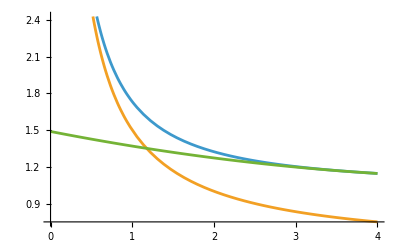

```mathematica
Plot[{Sqrt[1+ϵ^-1+ϵ^-2],y,y2},{ϵ,0,4}]
```

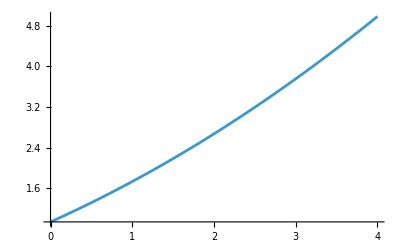

```mathematica
Plot[y2,{ϵ,0,4}]
```